# Squeezing - Process

## Last Updated: 11/12/2023

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

# General

## Values

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 14-bit amplitude scaling factor (ASF) to MHz (assuming 0x3FFF is 100%)*)
asfToAmplitudePCT=(1.*^2)/(Interpreter["HexInteger"]["3FFF"]);
```

### Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

### Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

### Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Phonon Conversion

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
```

### Dataset Processing

#### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Import[filenameDJ,{"Attributes","/arguments"}];

Return[{datasetRaw,parameterList}];
];
```

#### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
ThresholdCounts[dataset_List,countsColumn_Integer]:=Module[
{
(*find state discrimination threshold*)
countThreshold=FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"],
results=dataset
},
(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

#### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

### Batch Processing

```mathematica
(*(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS[filedir_,filekey_]:=Module[
{
(*actual data*)
(*datafile=ImportDatasetARTIQ[filedir,ToString[filekey]],*)
datafile,
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*import dataset*)
datafile=ImportDatasetARTIQ[filedir,ToString[filekey]];

(*extract heating time from parameter list*)
heatingTimeSeconds=datafile[[2]]["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[datafile[[1]]]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->datafile[[2]],
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datafile,datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
(*Remove[datafile];*)
ClearSystemCache[];

(*return dataset*)
Return[results];
];*)
```

```mathematica
(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS2[dataset_List,parameterList_Association]:=Module[
{
(*actual data*)
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*extract heating time from parameter list*)
heatingTimeSeconds=parameterList["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[dataset]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->parameterList,
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
ClearSystemCache[];

(*return dataset*)
Return[results];
];
```

# User Input

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2024-08\\2024-08-30";
```

## Validate User Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

# Run

## Import & Process

## tmp batch

```mathematica
directoryString="Z:\\motion\\Data\\2023-10-04";
```

```mathematica
ridArr=Join[
Range[36085,36089]
];
datafileArr=ImportDatasetARTIQ[directoryString,#]&/@ridArr;
```

$Aborted

```mathematica
xArr=#[[2]]["phase_antisqueeze_turns_list"][[1]]&/@datafileArr;
```

```mathematica
th0=ThresholdCounts[#[[1]],2]&/@datafileArr;
th1=CollateData[#,{1}]&/@th0;
```

```mathematica
freqCenter=Mean[Mean[Values[#[[;;,1]]]]&/@th1];
rsbYArr=#[[1]]&/@th1;rsbYArr=rsbYArr[[;;,2]];
bsbYArr=#[[2]]&/@th1;bsbYArr=bsbYArr[[;;,2]];
```

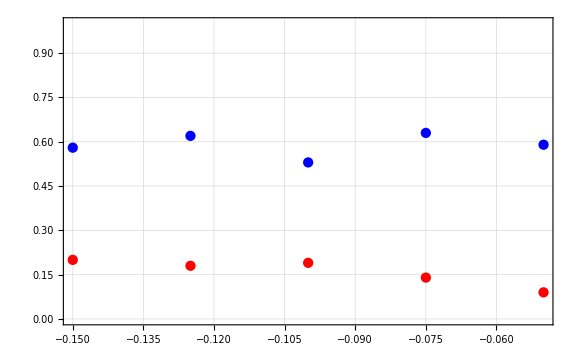

```mathematica
ListPlot[
{
Transpose[{xArr,rsbYArr}],
Transpose[{xArr,bsbYArr}]
},
PlotStyle->{Red,Blue},
PlotRange->{Automatic,{0,1}}
]
```

## ISA single point wsec/phase sweep

```mathematica
directoryString="Z:\\motion\\Data\\2024-08\\2024-08-23";
rid=71812;
```

### Import & Examine

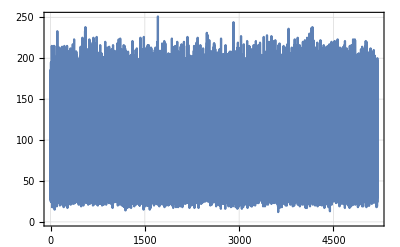
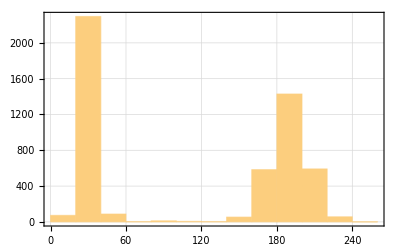
{-Graphics-,-Graphics-,(Missing[KeyAbsent,att_squeeze_db]
Missing[KeyAbsent,phase_antisqueeze_turns_list]
Missing[KeyAbsent,enable_antisqueezing])}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_squeeze_db"],
parameters["phase_antisqueeze_turns_list"],
parameters["enable_antisqueezing"]
}]
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,5,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process ratio*)
dsN=dsR;
dsN[[;;,2]]/=(dsB[[;;,2]]+1.*^-6);
```

### Fit

```mathematica
(*guess values*)
{xMax,yMax}=dsN[[First@Ordering[dsN[[;;,2]],-1]]];
phaseSPSweepGuess={
yMax,(*α*)
(*xMax(*β*)*)
1.0
};
```

```mathematica
(*phaseSPSweepModel=(α*Sin[2.π*(x+1.0*β)]+α)/2.;*)
phaseSPSweepModel=A*Cos[2.π*(x+1.0*ϕ)]+A;
```

```mathematica
phaseSPSweepConstraints={
0.<A<1.5,
0.<ϕ<1.
(*0.<δ<0.1*)
};
```

```mathematica
phaseSPSweepFit=NonlinearModelFit[
dsN,
Join[{phaseSPSweepModel,phaseSPSweepConstraints}],
Transpose[{{A,ϕ},phaseSPSweepGuess}],
x
];
```

```mathematica
phaseSPSweepFitPlot=Plot[
phaseSPSweepFit[ω],
{ω,dsN[[1,1]],dsN[[-1,1]]},
PlotStyle->{Black}
];
```

### Plot

```mathematica
dataPointsPlot=ListPlot[
{dsN},
PlotRange->{Full,Full},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["ISA Phase Sweep (Single Point)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{(*Red,Blue,*)Black}
];
```

```mathematica
(*format result table*)
phaseSPSweepParameterTable=Style[phaseSPSweepFit["ParameterConfidenceIntervalTable"],{Background->White}];
phaseSPSweepParameterTable[[1,1,1,3,{2,4}]]=1.-phaseSPSweepParameterTable[[1,1,1,3,{2,4}]];
```

### Show

```mathematica
{parameters["ampl_eggs_heating_rsb_pct"],
parameters["att_eggs_heating_db"],
parameters["time_eggs_heating_ms"]}
```

{0.,14.,1.}

| Estimate | Standard Error | Confidence Interval
A | 0.137051 | 0.0237596 | {0.0880131,0.186088}
ϕ | 1.1916×10^-7 | 0.0502745 | {0.103762,-0.103761}

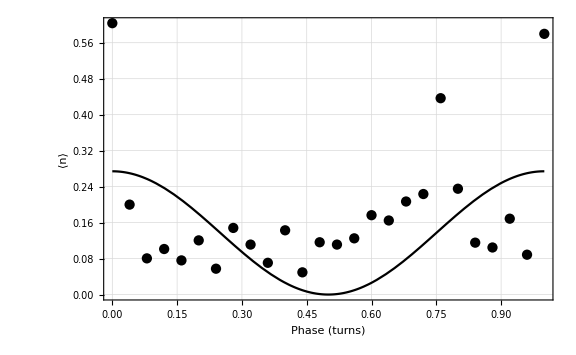

```mathematica
(*Style[phaseSPSweepFit["ParameterConfidenceIntervalTable"],{Background->White}]*)
phaseSPSweepParameterTable
Show[
dataPointsPlot,
phaseSPSweepFitPlot
]
```

## squeeze freq sweep

```mathematica
rid=69337;
```

### Import

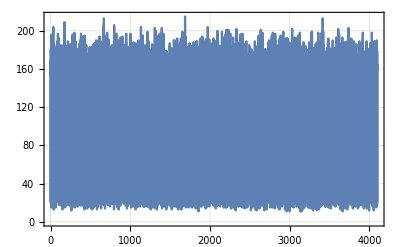
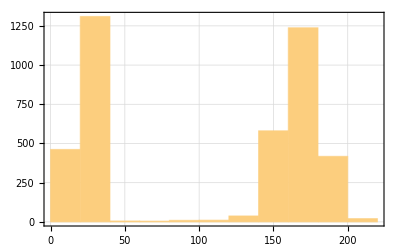
{-Graphics-,-Graphics-,(Missing[KeyAbsent,att_squeeze_db]
Missing[KeyAbsent,time_squeeze_us_list]
Missing[KeyAbsent,phase_antisqueeze_turns_list]
Missing[KeyAbsent,time_delay_us_list]
Missing[KeyAbsent,enable_squeezing]
Missing[KeyAbsent,enable_antisqueezing])}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["time_delay_us_list"],
parameters["enable_squeezing"],
parameters["enable_antisqueezing"]
}]
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,4,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,ftwToFrequencyMHz*1000.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];
(*freqCenter=1000;*)

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
(*process ratio*)
dsN=dsR;
dsN[[;;,2]]/=dsB[[;;,2]];
```

### Fit

```mathematica
(*guess values*)
sqFreqSweepGuess={
1.-#[[2]],(*α*)
#[[1]],(*β*)
1000./(First@parameters["time_delay_us_list"]),(*γ*)
1.0(*δ*)
}&[dsN[[First@Ordering[dsN[[;;,2]],1]]]]
```

{1.,1417.2,200.,1.}

```mathematica
sqFreqSweepModel=-α*Exp[-(f-β)^2./γ]+δ;
sqFreqSweepConstraints={
0.<α<1.5,
1410.<β<1430.,
0.<γ<10.,
0.1<δ<1.3
};
```

```mathematica
sqFreqSweepFit=NonlinearModelFit[
dsN,
Join[{sqFreqSweepModel,sqFreqSweepConstraints}],
Transpose[{{α,β,γ,δ},sqFreqSweepGuess}],
f
];
```

### Plot

```mathematica
summaryFigure={
ListPlot[
{
dsR,dsR,
dsB,dsB
},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (kHz)",{Black,Directive[15]}],
(*Style["Motional Ramsey (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]*)
Style["EGGS - DDS\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
Joined->{False,True,False,True},
PlotStyle->{
{Red},
{Red,Dashed},
{Blue},
{Blue,Dashed}
}
],
Show[
ListPlot[
{
dsN,
dsN
},
(*PlotRange->{Automatic,{0,1}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (kHz)",{Black,Directive[15]}],
(*Style["Motional Ramsey (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]*)
Style["EGGS - DDS\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
Joined->{False,True},
PlotStyle->{
{Black},
{Black,Dashed}
}
],
Plot[
sqFreqSweepFit[ω],
{ω,dsN[[1,1]],dsN[[-1,1]]},
PlotStyle->{Black}
]
]
};
```

### Show

| Estimate | Standard Error | Confidence Interval
α | 0.101576 | 0.037659 | {0.0261656,0.176987}
β | 1418.16 | 0.309821 | {1417.54,1418.78}
γ | 1.16283 | 1.14968 | {-1.13937,3.46502}
δ | 0.102395 | 0.0187317 | {0.0648854,0.139905}

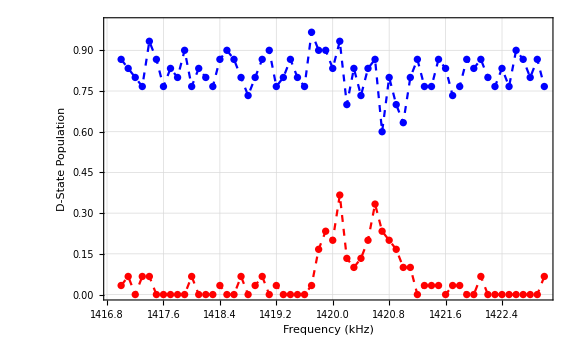
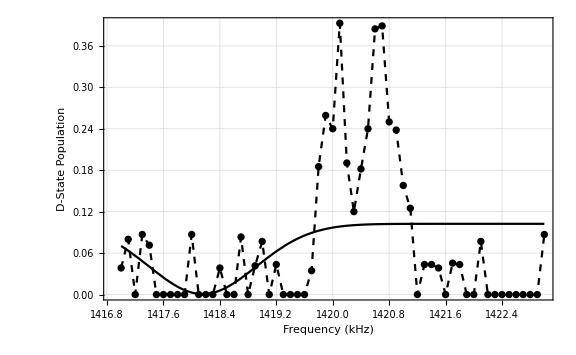

```mathematica
Style[sqFreqSweepFit["ParameterConfidenceIntervalTable"],{Background->White}]
summaryFigure
```

## squeeze freq sweep (sinc fit)

```mathematica
rid=62381;
```

### Import

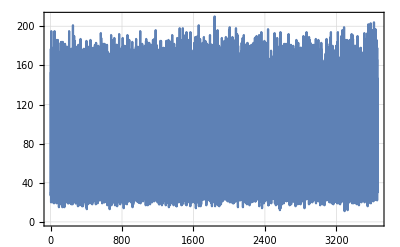
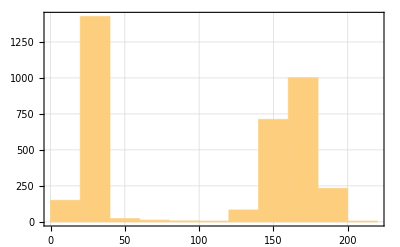
{-Graphics-,-Graphics-,(31.5
{1000.}
{0.}
{5.}
1
0)}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["time_delay_us_list"],
parameters["enable_squeezing"],
parameters["enable_antisqueezing"]
}]
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,3,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,ftwToFrequencyMHz*1000.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];
(*freqCenter=1000;*)

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
(*process ratio*)
dsN=dsR;
dsN[[;;,2]]/=dsB[[;;,2]];
```

### Fit

```mathematica
(*guess values*)
sqFreqSweepGuess={
1.-#[[2]],(*α*)
#[[1]],(*β*)
2.*π*1.*^-6*(First@parameters["time_squeeze_us_list"]),(*γ*)
1.0(*δ*)
}&[dsN[[First@Ordering[dsN[[;;,2]],1]]]]
```

{1.,1417.2,0.00628319,1.}

```mathematica
sqFreqSweepModel=α*Sinc[γ*(f-β)+0.0001]^2.+δ;
```

```mathematica
sqFreqSweepConstraints={
0.<α<1.5,
1410.<β<1430.,
(*0.<γ<10.,*)
0.<δ<0.1
};
```

```mathematica
sqFreqSweepFit=NonlinearModelFit[
dsN,
Join[{sqFreqSweepModel,sqFreqSweepConstraints}],
Transpose[{{α,β,γ,δ},sqFreqSweepGuess}],
f
];
```

### Plot

```mathematica
summaryFigure={
ListPlot[
{
dsR,dsR,
dsB,dsB
},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (kHz)",{Black,Directive[15]}],
(*Style["Motional Ramsey (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]*)
Style["EGGS - DDS\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
Joined->{False,True,False,True},
PlotStyle->{
{Red},
{Red,Dashed},
{Blue},
{Blue,Dashed}
}
],
Show[
ListPlot[
{
dsN,
dsN
},
(*PlotRange->{Automatic,{0,1}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (kHz)",{Black,Directive[15]}],
(*Style["Motional Ramsey (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]*)
Style["EGGS - DDS\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
Joined->{False,True},
PlotStyle->{
{Black},
{Black,Dashed}
}
],
Plot[
sqFreqSweepFit[ω],
{ω,dsN[[1,1]],dsN[[-1,1]]},
PlotStyle->{Black}
]
]
};
```

### Show

| Estimate | Standard Error | Confidence Interval
α | 0.284009 | 0.024187 | {0.235576,0.332443}
β | 1420.45 | 0.0432578 | {1420.37,1420.54}
γ | 2.49562 | 0.221137 | {2.0528,2.93844}
δ | 0.0162314 | 0.0091349 | {-0.0020609,0.0345237}

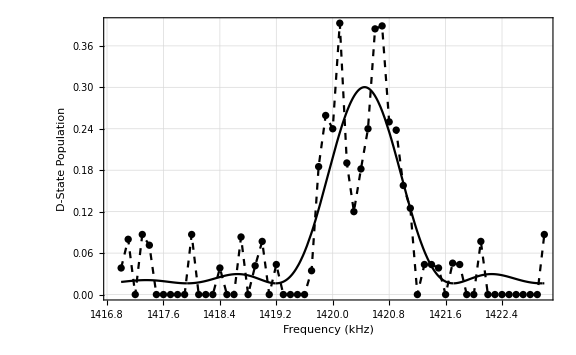
{-Graphics-,-Graphics-}

```mathematica
Style[sqFreqSweepFit["ParameterConfidenceIntervalTable"],{Background->White}]
summaryFigure
```

## antisqueeze phase sweep

```mathematica
rid=73141;
```

```mathematica
(*todo: errors*)
```

### Import

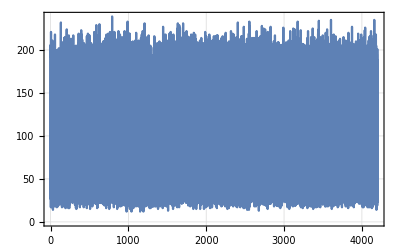
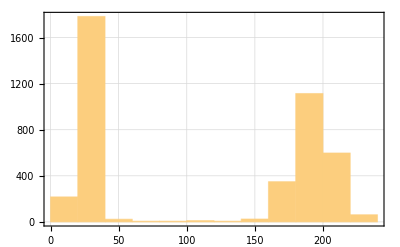

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,5,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,(*1./(2.^16.-1.)*)1.,1}];
(*datasetProcessed=ThresholdCounts[dataset[[;;,{1,4,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,4./1082.800,1}];*)
freqCenter=Mean[datasetProcessed[[;;,1]]];

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
(*phase unwrap*)
dsR[[;;,1]]=Mod[dsR[[;;,1]],1,-0.5];
dsB[[;;,1]]=Mod[dsB[[;;,1]],1,-0.5];
(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

### Fit

```mathematica
(*create fit function*)
fitFreq=1.0;
fitfunc=α*Sin[(fitFreq*π)*(ϕ-γ)]^2.+β;
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
fitfunc,
(*constraints*)
α>0.,β>0.,0.5>=γ>=-0.5
},
(*starting conditions*)
{
{α,0.8},
{γ,0.},
{β,0.}
},
ϕ
];
]
```

{0.0162029,Null}

```mathematica
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"],
{Background->White}
];
```

### Plot

```mathematica
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

```mathematica
summaryFigure={
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Antidisplace Phase (turns)",{Black,Directive[15]}],
(*Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]*)Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[parameters["time_ramsey_delay_us"]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black}
(*PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},{Above,Right}],
PlotLegends->{"S^†(ξ) S(ξ)","S(ξ)"}*)
],
Show[
ListPlot[
{dsN},
(*PlotRange->{Automatic,{0.,1.}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Antidisplace Phase (turns)",{Black,Directive[15]}],
(*Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]*)Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[parameters["time_ramsey_delay_us"]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Black}
],
fitPlot
]
};
```

### Show

| Estimate | Standard Error | Confidence Interval
α | 0.17431 | 0.0369544 | {0.0966718,0.251948}
γ | -0.461492 | 0.0351275 | {-0.535292,-0.387691}
β | 0.20551 | 0.0234662 | {0.156209,0.254811}

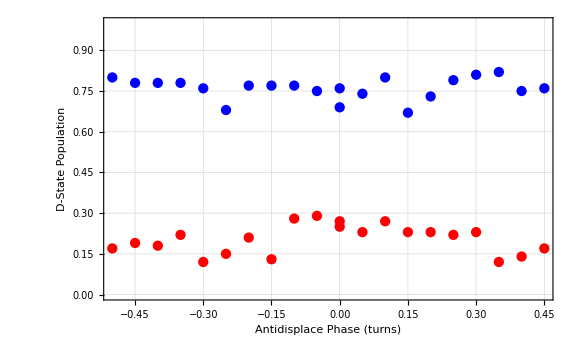
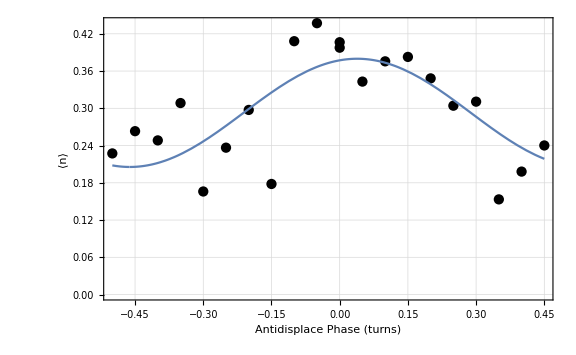

```mathematica
(*Max[dsRatio[[;;,2]]]
parameters["att_squeeze_db"]*)
fitParams
summaryFigure
```

## ***new*** antisqueeze freq sweep (ramsey)

```mathematica
rid=73141;
```

### Import

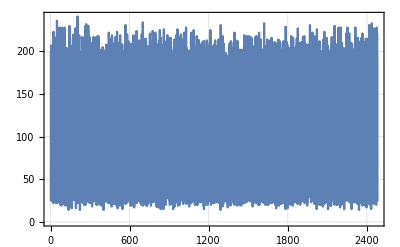
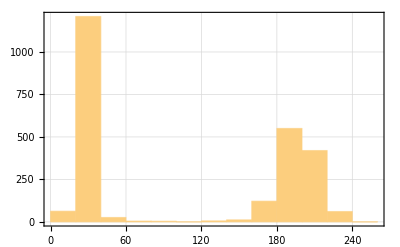

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,4,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1./(1.*^3(*kHz*)),1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];
```

```mathematica
(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
(*(*phase unwrap*)
dsR[[;;,1]]=Mod[dsR[[;;,1]],1,-0.5];
dsB[[;;,1]]=Mod[dsB[[;;,1]],1,-0.5];*)
(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

### Fit

```mathematica
(*create fit function*)
τ0=(2.*parameters["time_pulse_shape_rolloff_us"]+parameters["time_ramsey_delay_us"])*(1.*^-6);
fitfunc=α*Sin[(δ*1.*^3)*τ+ϕ]^2.+β;
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
fitfunc,
(*constraints*)
1.2>α>0.,β>0.(*,0.5>=ϕ>=-0.5*)
},
(*starting conditions*)
{
{α,0.7},
{ϕ,0.},
{β,0.3},
{τ,70.*^-3}
},
δ
];
]
```

{0.235336,Null}

```mathematica
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"],
{Background->White}
];
```

### Plot

```mathematica
fitPlot=
Plot[
fitRes[δ],
{δ,dsN[[1,1]],dsN[[-1,1]]}
];
```

```mathematica
summaryFigure={
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (kHz)",{Black,Directive[15]}],
Style["Motional Ramsey Fringes (T_Delay = "<>ToString[parameters["time_ramsey_delay_us"]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black}
(*PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},{Above,Right}],
PlotLegends->{"S^†(ξ) S(ξ)","S(ξ)"}*)
],
Show[
ListPlot[
{dsN},
(*PlotRange->{Automatic,{0.,1.}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (kHz)",{Black,Directive[15]}],
Style["Motional Ramsey Fringes (T_Delay = "<>ToString[parameters["time_ramsey_delay_us"]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Black}
],
fitPlot
]
};
```

### Show

1.04545

Missing[KeyAbsent,att_squeeze_db]

| Estimate | Standard Error | Confidence Interval
α | 0.364222 | 495.704 | {-1016.74,1017.47}
ϕ | -713.422 | 38306.3 | {-79311.5,77884.7}
β | 0.324267 | 247.85 | {-508.222,508.87}
τ | 0.0706599 | 0.0354425 | {-0.00206216,0.143382}

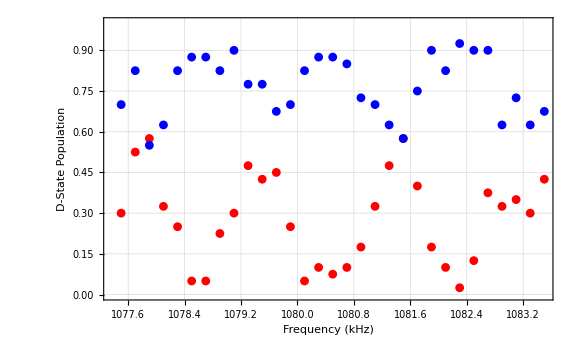
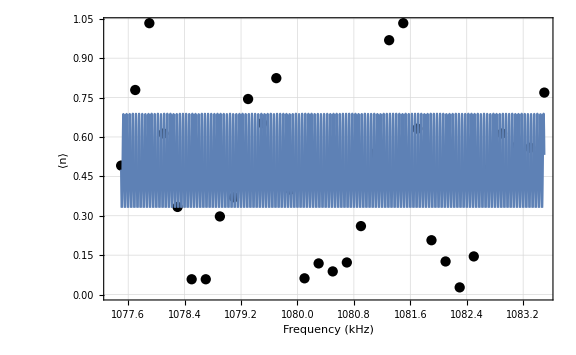

```mathematica
Max[dsRatio[[;;,2]]]
parameters["att_squeeze_db"]
fitParams
summaryFigure
```

## antisqueeze phase sweep w/freq sweep (2D)

```mathematica
rid=52317;
```

### Import

$Aborted

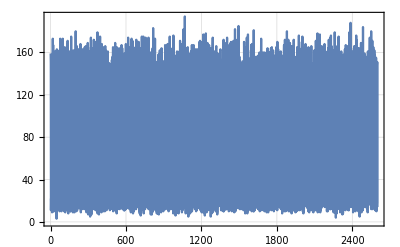
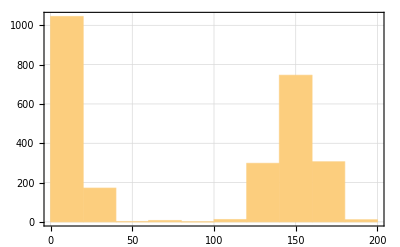

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,3,4,2}]],3];
datasetProcessed=Transpose[
Transpose[datasetProcessed]*{ftwToFrequencyMHz,ftwToFrequencyMHz*1000.,1./(2.^16.-1.),1}
];
freqCenter=Mean[datasetProcessed[[;;,1]]];
```

```mathematica
(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
(*phase unwrap*)
dsR[[;;,1]]=Mod[dsR[[;;,1]],1,-0.5];
dsB[[;;,1]]=Mod[dsB[[;;,1]],1,-0.5];
(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

### Fit

```mathematica
fitfunc=α*Sin[(1.*π)*ϕ+γ]^2.+β;
```

```mathematica
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
fitfunc,
{
{α,0.8},
{γ,0.},
{β,0.}
},
ϕ
];
]
```

{0.0009222,Null}

```mathematica
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"],
{Background->White}
];
```

### Plot

```mathematica
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

```mathematica
summaryFigure={
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Antidisplace Phase (turns)",{Black,Directive[15]}],
Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Blue,Black}
(*PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},{Above,Right}],
PlotLegends->{"S^†(ξ) S(ξ)","S(ξ)"}*)
],
Show[
ListPlot[
{dsN},
(*PlotRange->{Automatic,{0.,1.}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{Style["Antidisplace Phase (turns)",{Black,Directive[15]}],
Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Black}
],
fitPlot
]
};
```

### Show

0.645161

24.5

| Estimate | Standard Error | Confidence Interval
α | 0.644817 | 0.0613442 | {0.517597,0.772037}
γ | 0.03235 | 0.0475681 | {-0.0663003,0.131}
β | 0.0393933 | 0.0375653 | {-0.0385124,0.117299}

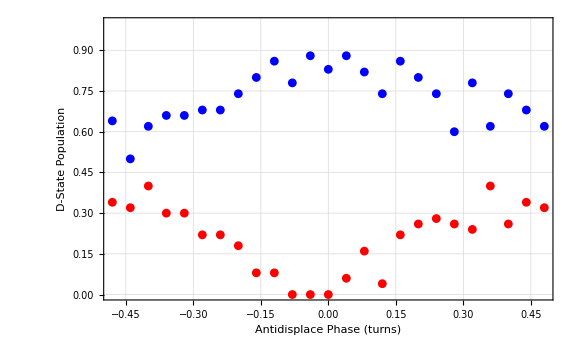
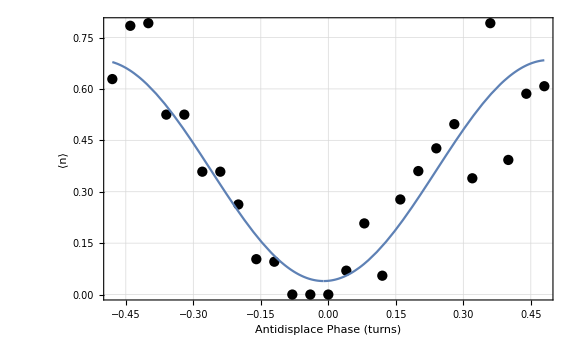

```mathematica
Max[dsRatio[[;;,2]]]
parameters["att_squeeze_db"]
fitParams
summaryFigure
```

## squeeze time sweep

```mathematica
rid=52276;
```

### Import

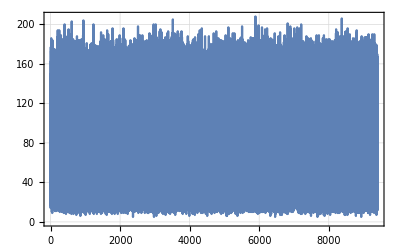
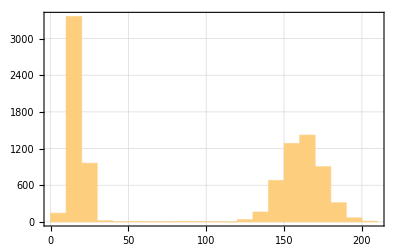
{-Graphics-,-Graphics-,{25.,{24.4565,50.,8.1087,11.1739,10.1522,23.4348,5.04348,4.02174,20.3696,44.8913,26.5,38.7609,47.9565,28.5435,41.8261,40.8043,43.8696,35.6957,32.6304,17.3043,25.4783,48.9783,46.9348,16.2826,34.6739,9.13043,7.08696,36.7174,37.7391,3.,31.6087,22.413,42.8478,18.3261,13.2174,30.587,14.2391,39.7826,19.3478,12.1957,45.913,27.5217,6.06522,21.3913,15.2609,29.5652,33.6522},{0.},{752.2},0}}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
}
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,5,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1./1000.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];

(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

InterpolatingFunction::dmval: Input value {0.827586} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.942308} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.859649} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### Plot

```mathematica
summaryFigure={
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Probability",{Black,Directive[15]}],None},
{Style["Displace Time (μs)",{Black,Directive[15]}],
Style["Displace Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Blue}
],
ListPlot[
{
dsN
},
PlotRange->{Automatic,{0.,1.}},
(*PlotRange->{Automatic,Full},*)
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{Style["Displace Time (μs)",{Black,Directive[15]}],
Style["Displace Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Black}
]
};
```

### Show

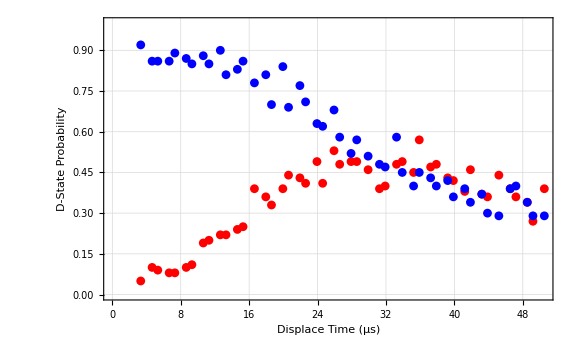
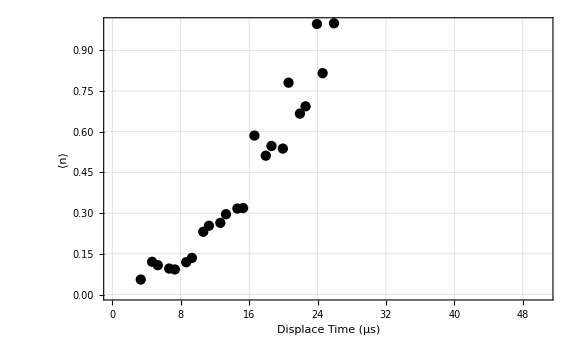

```mathematica
summaryFigure
```

## delay time sweep

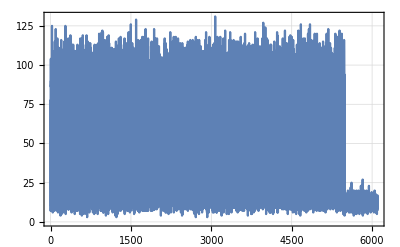
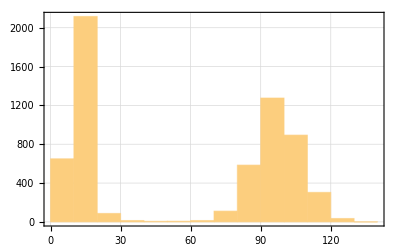

```mathematica
rid=41097;
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

```mathematica
dataset=dataset[[;;5700]];
```

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,6,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.*^-3,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
(*tmp remove*)
(*dsr[[;;,2]]=*)
(*tmp remove*)
```

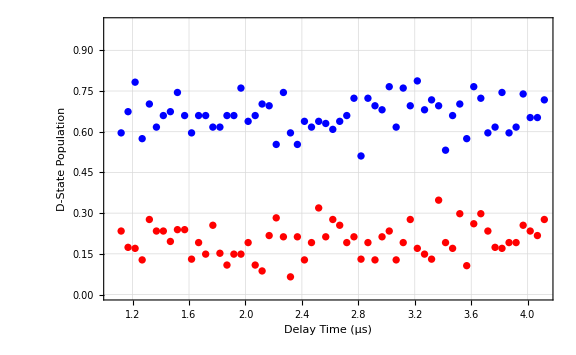

```mathematica
squeezeFreqSweep=ListPlot[
{dsR,dsB},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Delay Time (μs)",{Black,Directive[15]}],Style["Delay Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Blue}
(*PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},{Above,Right}],
PlotLegends->{"S^†(ξ) S(ξ)","S(ξ)"}*)
]
```

## tmp Readout time

```mathematica
rid=36295;

datafile=ImportDatasetARTIQ[directoryString,#]&[rid]
{dataset,parameters}=datafile;
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
}

dataset=dataset[[;;,{1,5,7,2}]]
dataset=Transpose[Transpose[dataset]*{ftwToFrequencyMHz,1./1000.,1./1000.,1}];
freqCenter=Mean[dataset[[;;,1]]];
dsR=Select[dataset,#[[1]]<freqCenter&][[;;,{3,4}]];
dsB=Select[dataset,#[[1]]>=freqCenter&][[;;,{3,4}]];

dsR=ThresholdCounts[dsR,2];
dsR=Values[CollateData[dsR,{1}]];
dsR=SortBy[dsR,First];

dsB=ThresholdCounts[dsB,2];
dsB=Values[CollateData[dsB,{1}]];
dsB=SortBy[dsB,First];
```

{4.,{30.},{0.},{1542.5},1}

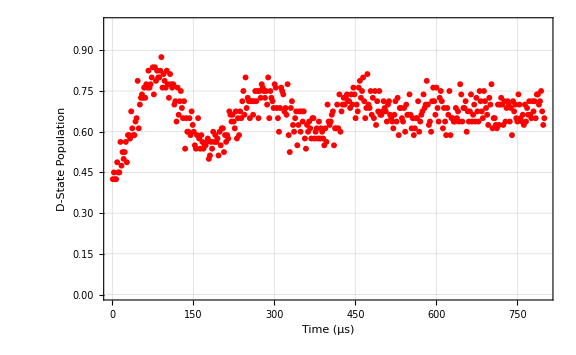

```mathematica
yzsg1=ListPlot[
{(*dsRA,dsRS,*)dsB},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Time (μs)",{Black,Directive[15]}],Style["Squeeze Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Black}(*,
PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},{Above,Right}],
PlotLegends->{"S^†(ξ) S(ξ)","S(ξ)"}*)
]
```

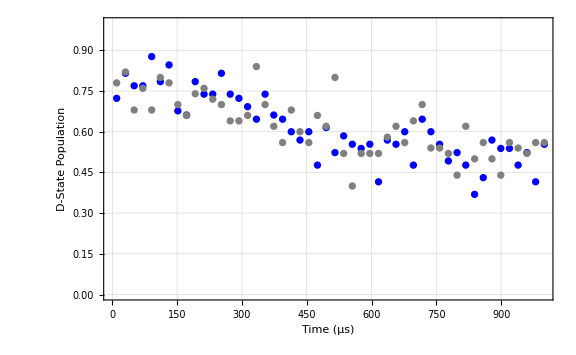

```mathematica
ListPlot[
{dsRB,dsBB},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Time (μs)",{Black,Directive[15]}],Style["Squeeze Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Blue,Gray}(*,
PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},Above],
PlotLegends->{"S(ξ) S^†(ξ)","S(ξ)"}*)
]
```

## 2d sweep

```mathematica
rid=35715;
```

```mathematica
datafile=ImportDatasetARTIQ[directoryString,#]&[rid];
{dataset,parameters}=datafile;
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"]
}

dataset=dataset[[;;,{1,6,4,2}]];
dataset=Transpose[Transpose[dataset]*{ftwToFrequencyMHz,1./1000.(*ftwToFrequencyMHz*),1/(2^15-1),1}];
freqCenter=Mean[dataset[[;;,1]]];
dsR=Select[dataset,#[[1]]<freqCenter&][[;;,{2,3,4}]];
dsB=Select[dataset,#[[1]]>=freqCenter&][[;;,{2,3,4}]];
```

{11.,{50.}}

```mathematica
dsR=ThresholdCounts[dsR,-1];
dsR=CollateData[dsR,{2,1}];
dsR=Values[#][[;;,{1,3}]]&/@dsR;
(*dsR=SortBy[dsR,First];*)
```

```mathematica
dsB=ThresholdCounts[dsB,-1];
dsB=CollateData[dsB,{2,1}];
dsB=Values[#][[;;,{1,3}]]&/@dsB;
```

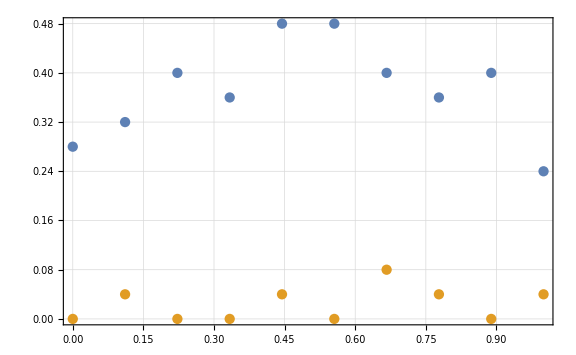

```mathematica
kk0=Values[Max[#[[;;,2]]]&/@dsR];
kk1=Values[Min[#[[;;,2]]]&/@dsR];
ListPlot[{Transpose[{Keys[dsR],kk0}],Transpose[{Keys[dsR],kk1}]}]
```

```mathematica
kk2=Values[Max[#[[;;,2]]]&/@dsR];
kk3=Values[Min[#[[;;,2]]]&/@dsR];
ListPlot[{Transpose[{Keys[dsR],kk0}],Transpose[{Keys[dsR],kk1}]}]
```

-Graphics-

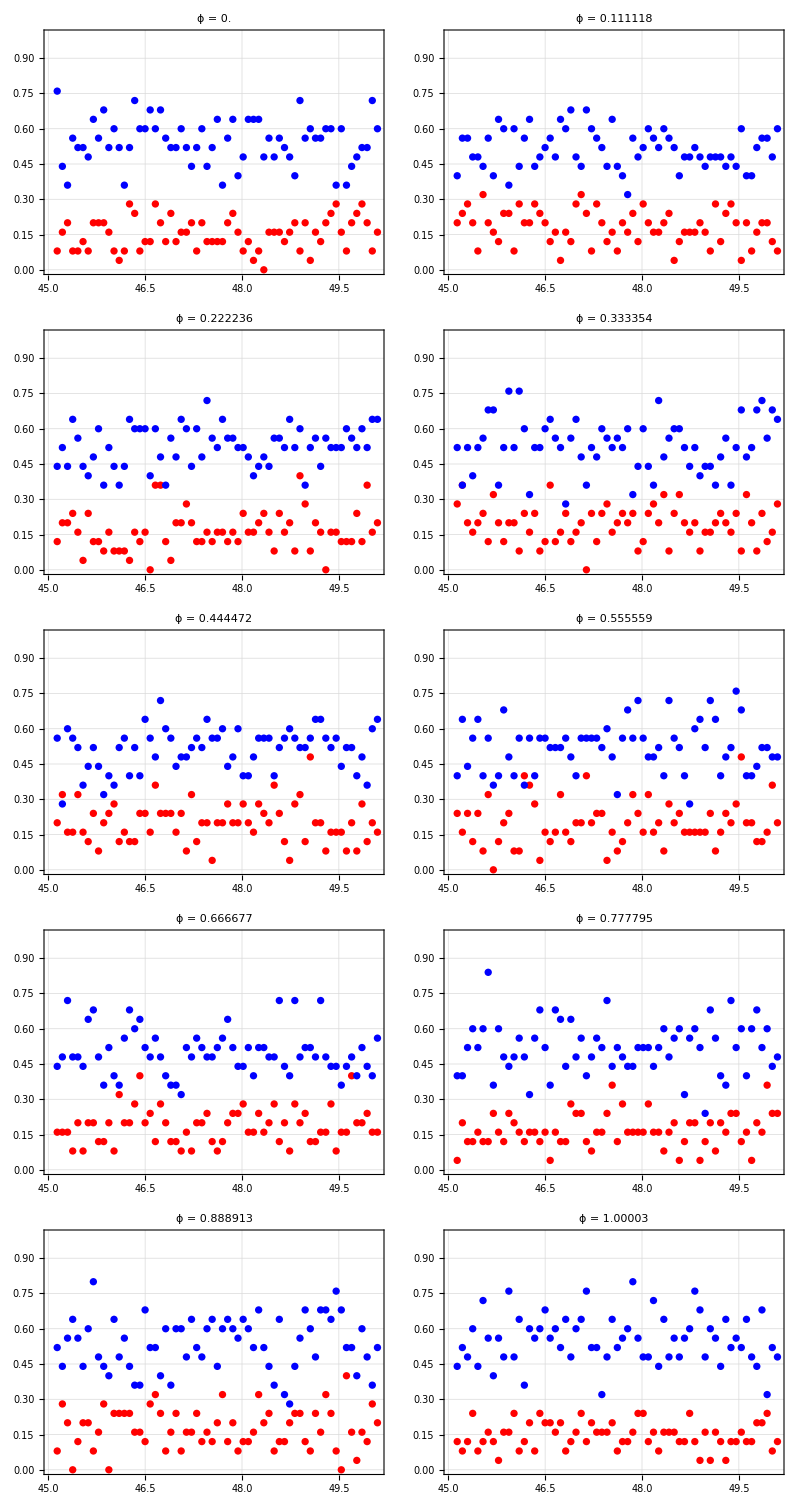

```mathematica
mzdp0=ListPlot[
{dsR[[#]],dsB[[#]]},
PlotRange->{Automatic,{0,1}},
PlotStyle->{Red,Blue},
PlotLabel->Style["ϕ = "<>ToString[Keys[dsR][[#]]],{FontSize->20}]
]&/@Range[Length[dsR]];

mzdp0=ArrayReshape[mzdp0,{5,2}];
Grid[mzdp0]
```

## sideband readout

```mathematica
rid=35715;
```

```mathematica
datafile=ImportDatasetARTIQ[directoryString,#]&[rid];
{dataset,parameters}=datafile;
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"]
}

dataset=dataset[[;;,{1,6,4,2}]];
dataset=Transpose[Transpose[dataset]*{ftwToFrequencyMHz,1./1000.(*ftwToFrequencyMHz*),1/(2^15-1),1}];
freqCenter=Mean[dataset[[;;,1]]];
dsR=Select[dataset,#[[1]]<freqCenter&][[;;,{2,3,4}]];
dsB=Select[dataset,#[[1]]>=freqCenter&][[;;,{2,3,4}]];
```

{11.,{50.}}

```mathematica
dsR=ThresholdCounts[dsR,-1];
dsR=CollateData[dsR,{2,1}];
dsR=Values[#][[;;,{1,3}]]&/@dsR;
(*dsR=SortBy[dsR,First];*)
```

```mathematica
dsB=ThresholdCounts[dsB,-1];
dsB=CollateData[dsB,{2,1}];
dsB=Values[#][[;;,{1,3}]]&/@dsB;
```

```mathematica
kk0=Values[Max[#[[;;,2]]]&/@dsR];
kk1=Values[Min[#[[;;,2]]]&/@dsR];
ListPlot[{Transpose[{Keys[dsR],kk0}],Transpose[{Keys[dsR],kk1}]}]
```

-Graphics-

## tickle freq sweep

```mathematica
rid=73110;
```

## Process

### Import

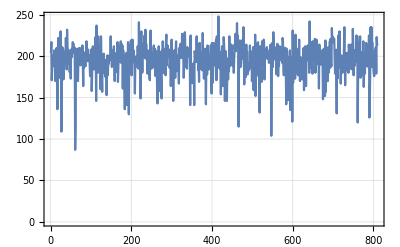
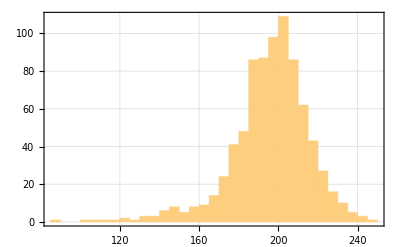
{-Graphics-,-Graphics-,(5.)}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_tickle_db"]
}]
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*datasetProcessed=ThresholdCounts[dataset[[;;,{1,2}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];
(*freqCenter=1000;*)*)
```

```mathematica
(*process dataset*)
datasetProcessed=Transpose[
Transpose[dataset[[;;,{1,2}]]]
*{ftwToFrequencyMHz*(1.*^3),1}
];
datasetProcessed=Values[CollateData[datasetProcessed,{1}]];
```

### Plot

```mathematica
summaryFigure=ListPlot[
{
datasetProcessed
},
PlotRange->{Automatic,Full},
FrameLabel->{ 
{Style["Counts (arb.)",{Black,Directive[15]}],None},
{Style["Frequency (kHz)",{Black,Directive[15]}],
Style["Tickle Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
Joined->{False,True,False,True},
PlotStyle->{
{Red},
{Red,Dashed},
{Blue},
{Blue,Dashed}
}
];
```

## Show

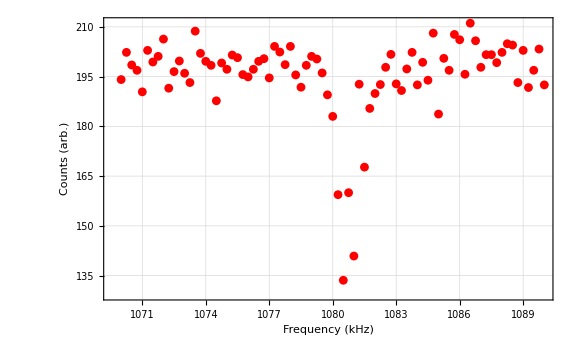

```mathematica
summaryFigure
```

## tickle freq sweep (timestamped)

```mathematica
rid=54661;
```

## Process

### custom import func bc i’m lazy

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQTimestamped[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
timestampedCounts,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
timestampedCounts=Import[filenameDJ,{"/datasets/timestamped_counts"}];
parameterList=Import[filenameDJ,{"Attributes","/arguments"}];

Return[{datasetRaw,timestampedCounts,parameterList}];
];
```

### Import

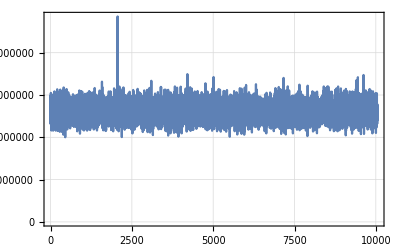
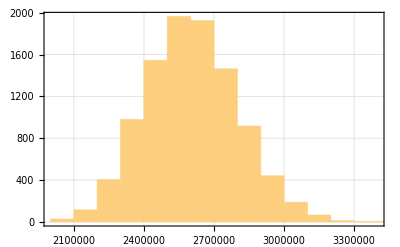
{-Graphics-,-Graphics-,(19.)}

```mathematica
datafile=ImportDatasetARTIQTimestamped[directoryString,ToString[#]]&[rid];
{dataset,timestampedCounts,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_tickle_db"]
}]
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*convert units*)
timestampedCountsus=timestampedCounts*(1.*^-3)*UnitStep[timestampedCounts];
datasetConverted=Transpose[
Transpose[dataset[[;;,{1,2,3,4}]]]
*{ftwToFrequencyMHz*(1.*^3),1.*^-3,asfToAmplitudePCT,1.*^-3}
];
```

```mathematica
(*select axes config we want*)
datasetProcessed=Join[datasetConverted[[;;,{1}]],timestampedCountsus,2];
```

```mathematica
(*datasetProcessed=Values[CollateData[datasetProcessed,{1}]];*)
```

```mathematica
th0=GroupBy[datasetProcessed,First]//KeySort;
```

```mathematica
th0//Keys
```

{1256.7,1248.7,1244.1,1249.3,1250.5,1255.3,1248.8,1250.1,1258.1,1260.2,1260.8,1251.6,1252.4,1254.7,1254.4,1251.4,1247.7,1260.7,1253.3,1256.3,1248.9,1256.1,1244.5,1257.8,1258.8,1255.7,1259.,1252.,1255.9,1243.3,1261.,1250.,1257.7,1247.,1261.8,1251.1,1258.3,1246.4,1253.4,1245.,1243.6,1253.8,1262.5,1246.9,1250.9,1244.7,1257.1,1259.5,1258.2,1262.2,1245.3,1258.5,1260.,1254.3,1256.4,1248.3,1252.9,1262.3,1260.5,1255.6,1249.6,1258.6,1250.7,1255.1,1252.8,1249.5,1243.4,1253.6,1245.5,1259.6,1243.,1260.3,1254.5,1244.8,1246.6,1260.1,1253.2,1245.9,1244.3,1243.1,1260.6,1256.5,1247.3,1254.,1255.5,1262.6,1252.5,1250.2,1259.9,1243.9,1261.9,1242.7,1259.2,1245.7,1247.4,1246.2,1259.7,1252.2,1262.1,1254.9,1243.8,1243.2,1242.8,1247.8,1248.5,1260.9,1242.6,1247.6,1244.4,1256.9,1249.4,1259.4,1256.2,1257.,1245.4,1258.7,1253.7,1261.4,1248.1,1244.2,1242.9,1248.4,1254.2,1254.8,1250.3,1261.5,1255.8,1244.,1254.6,1245.2,1257.2,1256.8,1256.,1252.3,1248.6,1251.7,1262.4,1249.1,1254.1,1243.5,1261.7,1251.2,1253.1,1258.9,1247.2,1257.3,1249.9,1244.6,1250.4,1262.,1260.4,1253.5,1252.7,1261.6,1259.3,1249.8,1246.3,1247.1,1252.1,1259.8,1259.1,1247.5,1246.1,1257.9,1261.3,1251.3,1243.7,1251.9,1257.6,1245.8,1244.9,1258.4,1255.4,1261.2,1245.1,1249.7,1250.6,1249.,1257.5,1257.4,1253.9,1252.6,1253.,1246.7,1251.5,1261.1,1247.9,1246.8,1256.6,1255.,1246.,1245.6,1258.,1250.8,1246.5,1249.2,1248.2,1255.2,1251.,1251.8,1248.}

```mathematica
timestampedCounts//Dimensions
```

{10050,200}

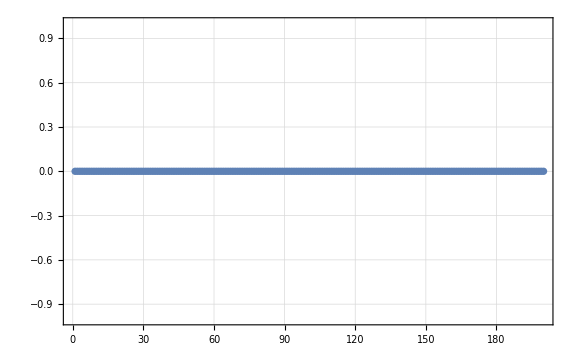

```mathematica
ListPlot[datasetProcessed[[#,2;;]]]&[1011]
```

### Plot

```mathematica
summaryFigure=ListPlot[
{
datasetProcessed
},
PlotRange->{Automatic,Full},
FrameLabel->{ 
{Style["Counts (arb.)",{Black,Directive[15]}],None},
{Style["Frequency (kHz)",{Black,Directive[15]}],
Style["Tickle Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
Joined->{False,True,False,True},
PlotStyle->{
{Red},
{Red,Dashed},
{Blue},
{Blue,Dashed}
}
];
```

## Show

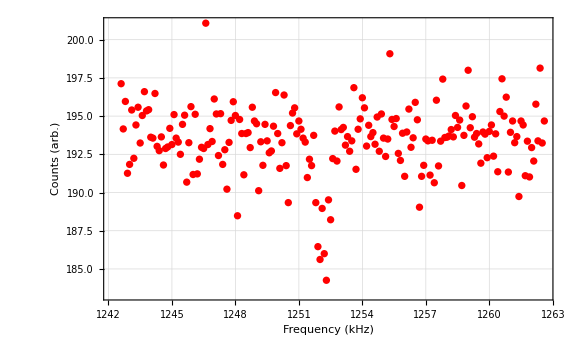

```mathematica
summaryFigure
```

## Show

```mathematica
(*timestampedCountsus=timestampedCounts*1.*^-6;
datasetTimestamped=dataset;*)
```

```mathematica
datasetConverted=datasetTimestamped
```

```mathematica
{ftwToFrequencyMHz,1.*^-6,1,1}*#&/@datasetTimestamped[[;;5,;;4]]
```

{{5.39577×10^6,3.35541×10^6,57.,999999.},{5.3511×10^6,3.03556×10^6,57.,999999.},{5.35926×10^6,3.06692×10^6,57.,999999.},{5.41123×10^6,3.06898×10^6,57.,999999.},{5.35067×10^6,3.16277×10^6,57.,999999.}}

```mathematica
resFull[[;;3,;;4]]//MatrixForm
```

(5.39577×10^6 | 3.35541×10^6 | 57. | 999999.
5.3511×10^6 | 3.03556×10^6 | 57. | 999999.
5.35926×10^6 | 3.06692×10^6 | 57. | 999999.)

```mathematica
resFull//Dimensions
```

{10050,204}

```mathematica
resFull[[1,;;6]]
```

{5.39577×10^6,3.35541×10^6,57.,999999.,7582,81977}

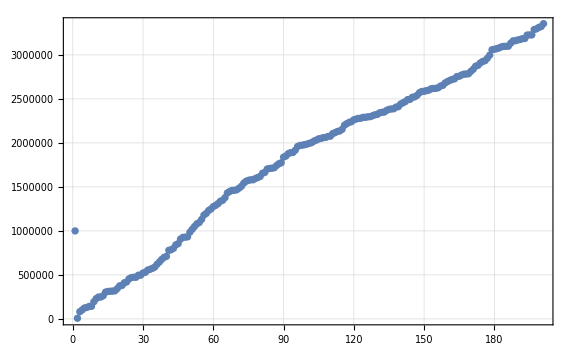

```mathematica
ListPlot[resFull[[1,4;;]]]
```